```mathematica
(* Figure out the rotation that puts the signal and idler into the pump coordinates. Here θ is the opening angle and ϕ is the azimuthal angle.
*)
RotX:= {{1, 0, 0},{0, Cos[θ],Sin[θ]}, {0, -Sin[θ], Cos[θ]}}
RotZ:={{ Cos[ϕ],Sin[ϕ], 0}, {-Sin[ϕ], Cos[ϕ], 0}, {0,0,1}}
RotY := {{ Cos[γ],0, -Sin[γ]}, {0,1,0},  {Sin[γ],0,  Cos[γ]}}

RotX:= {{1, 0, 0},{0, Cos[θ],-Sin[θ]}, {0, Sin[θ], Cos[θ]}}
RotZ:={{ Cos[ϕ],-Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0}, {0,0,1}}
RotY := {{ Cos[γ],0, Sin[γ]}, {0,1,0},  {-Sin[γ],0,  Cos[γ]}}

RotZLab := RotY;
RotXLab := RotZ;
RotYLab := RotX;

RotTrans=RotX . RotZ
RotPumpwrtXtal = RotX.RotZ

Expand[RotXLab.{x1,y1,z1}//.{z1->Cos[Subscript[γ, p]]*x -Sin[Subscript[γ, p]]*z,x1-> y, y1-> Sin[Subscript[γ, p]]*x -Cos[Subscript[γ, p]]*z}]
```

{{Cos[ϕ],-Sin[ϕ],0},{Cos[θ] Sin[ϕ],Cos[θ] Cos[ϕ],-Sin[θ]},{Sin[θ] Sin[ϕ],Cos[ϕ] Sin[θ],Cos[θ]}}

{{Cos[ϕ],-Sin[ϕ],0},{Cos[θ] Sin[ϕ],Cos[θ] Cos[ϕ],-Sin[θ]},{Sin[θ] Sin[ϕ],Cos[ϕ] Sin[θ],Cos[θ]}}

{y Cos[ϕ]+z Cos[γ_p] Sin[ϕ]-x Sin[ϕ] Sin[γ_p],-z Cos[ϕ] Cos[γ_p]+y Sin[ϕ]+x Cos[ϕ] Sin[γ_p],x Cos[γ_p]-z Sin[γ_p]}

```mathematica
(* We can use the fact that Subscript[ϕ, i]= Subscript[ϕ, s]+π to simplify things somewhat. Here are the coordinate transformations for the signal and idler. Eventually, these terms will include the walkoff angles for the signal, idler, and pump. For now, this is more tractable.*)
(*Subscript[x, s] := Cos[Subscript[ϕ, s]]*x + Cos[Subscript[θ, s]]*Sin[Subscript[ϕ, s]]*y + Sin[Subscript[θ, s]]*Sin[Subscript[ϕ, s]]*z
Subscript[y, s]:= -Sin[Subscript[ϕ, s]]*x + Cos[Subscript[θ, s]]*Cos[Subscript[ϕ, s]]*y + Sin[Subscript[θ, s]]*Cos[Subscript[ϕ, s]]*z
Subscript[z, s]:= -Sin[Subscript[θ, s]]*y + Cos[Subscript[θ, s]]*z

Subscript[x, i] := -Cos[Subscript[ϕ, s]]*x - Cos[Subscript[θ, i]]*Sin[Subscript[ϕ, s]]*y - Sin[Subscript[θ, i]]*Sin[Subscript[ϕ, s]]*z
Subscript[y, i]:= Sin[Subscript[ϕ, s]]*x - Cos[Subscript[θ, i]]*Cos[Subscript[ϕ, s]]*y - Sin[Subscript[θ, i]]*Cos[Subscript[ϕ, s]]*z
Subscript[z, i]:= -Sin[Subscript[θ, i]]*y + Cos[Subscript[θ, i]]*z

Subscript[x, p] := x + Tan[Subscript[ρ, px]]*z
Subscript[y, p] :=  y+ Tan[Subscript[ρ, py]]*z*)

(*Made a mistake in my coordinate transforms before. Now I need to fix them up.*)

Subscript[x, s] := Cos[Subscript[ϕ, s]]*x -Sin[Subscript[ϕ, s]]*y 
Subscript[y, s]:= Cos[Subscript[θ, s]]*Sin[Subscript[ϕ, s]]*x + Cos[Subscript[θ, s]]*Cos[Subscript[ϕ, s]]*y - Sin[Subscript[θ, s]]*z
Subscript[z, s]:=Sin[Subscript[θ, s]]*Sin[Subscript[ϕ, s]]*x + Sin[Subscript[θ, s]]*Cos[Subscript[ϕ, s]] + Cos[Subscript[θ, s]]*z

rulescoord :={Subscript[θ, s]->Subscript[θ, i], Subscript[ϕ, s]->Subscript[ϕ, s]+π}
Subscript[x, i] := Subscript[x, s]/.rulescoord
Subscript[y, i]:= Subscript[y, s]/.rulescoord
Subscript[z, i]:= Subscript[z, s]/.rulescoord

(* Include pump walkoff in a uniaxial crystal configuration. The center of the Gaussian beam translates vertically upward along the x dir. Use small angle approx to replace Tan[ Subscript[ρ, px]] with  Subscript[ρ, px].
*)
Subscript[x, p] := x + Subscript[ρ, px]*z
Subscript[y, p]:= y


(*Here is the argument in the exponential that we will want to integrate over wrt to x, y, and z.
*)
```

```mathematica
Arg1=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, i])(Subscript[x, i]^2+Subscript[y, i]^2)-1/(2*Subscript[q, p])*(Subscript[x, p]^2+Subscript[y, p]^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z)
```

-((-x Cos[ϕ_s]+y Sin[ϕ_s])^2+(-y Cos[θ_i] Cos[ϕ_s]-z Sin[θ_i]-x Cos[θ_i] Sin[ϕ_s])^2)/(2 q_i)-((x Cos[ϕ_s]-y Sin[ϕ_s])^2+(y Cos[θ_s] Cos[ϕ_s]-z Sin[θ_s]+x Cos[θ_s] Sin[ϕ_s])^2)/(2 q_s)-ⅈ (x ΔK_x+y ΔK_y+z ΔK_z)-(y^2+(x+z ρ_px)^2)/(2 q_p)

```mathematica
CompleteSquare[f_,x_]:=Module[{a,b,c},
{c,b,a}=CoefficientList[f,x];
a(x+b/2/a)^2+Simplify[(c-b^2/4/a)]
]
```

```mathematica
(* First we complete the square wrt to x. This makes it easier to analytically carry out the integration.
*)
Arg1 = CompleteSquare[Arg1, x]
```

(-Cos[ϕ_s]^2/(2 q_i)-(Cos[θ_i]^2 Sin[ϕ_s]^2)/(2 q_i)-1/(2 q_p)-Cos[ϕ_s]^2/(2 q_s)-(Cos[θ_s]^2 Sin[ϕ_s]^2)/(2 q_s)) (x+((y Cos[ϕ_s] Sin[ϕ_s])/q_i-(y Cos[θ_i]^2 Cos[ϕ_s] Sin[ϕ_s])/q_i-(z Cos[θ_i] Sin[θ_i] Sin[ϕ_s])/q_i+(y Cos[ϕ_s] Sin[ϕ_s])/q_s-(y Cos[θ_s]^2 Cos[ϕ_s] Sin[ϕ_s])/q_s+(z Cos[θ_s] Sin[θ_s] Sin[ϕ_s])/q_s-ⅈ ΔK_x-(z ρ_px)/q_p)/(2 (-Cos[ϕ_s]^2/(2 q_i)-(Cos[θ_i]^2 Sin[ϕ_s]^2)/(2 q_i)-1/(2 q_p)-Cos[ϕ_s]^2/(2 q_s)-(Cos[θ_s]^2 Sin[ϕ_s]^2)/(2 q_s))))^2+1/4 (-(2 y^2 Cos[θ_i]^2 Cos[ϕ_s]^2)/q_i-(2 z^2 Sin[θ_i]^2)/q_i-(2 y z Cos[ϕ_s] Sin[2 θ_i])/q_i-(2 y^2 Sin[ϕ_s]^2)/q_i-(2 y^2)/q_p-(2 y^2 Cos[θ_s]^2 Cos[ϕ_s]^2)/q_s-(2 z^2 Sin[θ_s]^2)/q_s+(2 y z Cos[ϕ_s] Sin[2 θ_s])/q_s-(2 y^2 Sin[ϕ_s]^2)/q_s-4 ⅈ y ΔK_y-4 ⅈ z ΔK_z-(2 z^2 ρ_px^2)/q_p+(2 (Sin[θ_i] (z Cos[θ_i]-y Cos[ϕ_s] Sin[θ_i]) Sin[ϕ_s] q_p q_s+q_i (q_p (-Sin[θ_s] (z Cos[θ_s]+y Cos[ϕ_s] Sin[θ_s]) Sin[ϕ_s]+ⅈ q_s ΔK_x)+z q_s ρ_px))^2)/(q_i q_p q_s ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))))

```mathematica
(* Now, the term in the b*(x-a)^2 term integrates to a constant*)
xconst:= Simplify[√π/-(-Cos[Subscript[ϕ, s]]^2/(2 Subscript[q, i])-(Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2)/(2 Subscript[q, i])-1/(2 Subscript[q, p])-Cos[Subscript[ϕ, s]]^2/(2 Subscript[q, s])-(Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2)/(2 Subscript[q, s]))]
 
(*now we can do the remaining integral wrt y and complete the square agaim*)
yArg:= Simplify[+1/4 (-(2 y^2 Cos[Subscript[θ, i]]^2 Cos[Subscript[ϕ, s]]^2)/Subscript[q, i]-(2 z^2 Sin[Subscript[θ, i]]^2)/Subscript[q, i]-(2 y z Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, i]])/Subscript[q, i]-(2 y^2 Sin[Subscript[ϕ, s]]^2)/Subscript[q, i]-(2 y^2)/Subscript[q, p]-(2 y^2 Cos[Subscript[θ, s]]^2 Cos[Subscript[ϕ, s]]^2)/Subscript[q, s]-(2 z^2 Sin[Subscript[θ, s]]^2)/Subscript[q, s]+(2 y z Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]])/Subscript[q, s]-(2 y^2 Sin[Subscript[ϕ, s]]^2)/Subscript[q, s]-4 ⅈ y Subscript[ΔK, y]-4 ⅈ z Subscript[ΔK, z]-(2 z^2 Subscript[ρ, px]^2)/Subscript[q, p]+(2 (Sin[Subscript[θ, i]] (z Cos[Subscript[θ, i]]-y Cos[Subscript[ϕ, s]] Sin[Subscript[θ, i]]) Sin[Subscript[ϕ, s]] Subscript[q, p] Subscript[q, s]+Subscript[q, i] (Subscript[q, p] (-Sin[Subscript[θ, s]] (z Cos[Subscript[θ, s]]+y Cos[Subscript[ϕ, s]] Sin[Subscript[θ, s]]) Sin[Subscript[ϕ, s]]+ⅈ Subscript[q, s] Subscript[ΔK, x])+z Subscript[q, s] Subscript[ρ, px]))^2)/(Subscript[q, i] Subscript[q, p] Subscript[q, s] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))))]


(*Simplify[yArg]*)

yArg2=CompleteSquare[yArg,y]
```

(-(Cos[θ_i]^2 Cos[ϕ_s]^2)/(2 q_i)-Sin[ϕ_s]^2/(2 q_i)-1/(2 q_p)-(Cos[θ_s]^2 Cos[ϕ_s]^2)/(2 q_s)-Sin[ϕ_s]^2/(2 q_s)+(Cos[ϕ_s]^2 Sin[θ_i]^2 Sin[θ_s]^2 Sin[ϕ_s]^2 q_p)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))+(Cos[ϕ_s]^2 Sin[θ_s]^4 Sin[ϕ_s]^2 q_i q_p)/(2 q_s ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))+(Cos[ϕ_s]^2 Sin[θ_i]^4 Sin[ϕ_s]^2 q_p q_s)/(2 q_i ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))) (y+(-(z Cos[ϕ_s] Sin[2 θ_i])/(2 q_i)+(z Cos[ϕ_s] Sin[2 θ_s])/(2 q_s)+(z Cos[θ_s] Cos[ϕ_s] Sin[θ_i]^2 Sin[θ_s] Sin[ϕ_s]^2 q_p)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(z Cos[θ_i] Cos[ϕ_s] Sin[θ_i] Sin[θ_s]^2 Sin[ϕ_s]^2 q_p)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))+(z Cos[θ_s] Cos[ϕ_s] Sin[θ_s]^3 Sin[ϕ_s]^2 q_i q_p)/(q_s ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))-(z Cos[θ_i] Cos[ϕ_s] Sin[θ_i]^3 Sin[ϕ_s]^2 q_p q_s)/(q_i ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))-(ⅈ Cos[ϕ_s] Sin[θ_s]^2 Sin[ϕ_s] q_i q_p ΔK_x)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(ⅈ Cos[ϕ_s] Sin[θ_i]^2 Sin[ϕ_s] q_p q_s ΔK_x)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-ⅈ ΔK_y-(z Cos[ϕ_s] Sin[θ_s]^2 Sin[ϕ_s] q_i ρ_px)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(z Cos[ϕ_s] Sin[θ_i]^2 Sin[ϕ_s] q_s ρ_px)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))/(2 (-(Cos[θ_i]^2 Cos[ϕ_s]^2)/(2 q_i)-Sin[ϕ_s]^2/(2 q_i)-1/(2 q_p)-(Cos[θ_s]^2 Cos[ϕ_s]^2)/(2 q_s)-Sin[ϕ_s]^2/(2 q_s)+(Cos[ϕ_s]^2 Sin[θ_i]^2 Sin[θ_s]^2 Sin[ϕ_s]^2 q_p)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))+(Cos[ϕ_s]^2 Sin[θ_s]^4 Sin[ϕ_s]^2 q_i q_p)/(2 q_s ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))+(Cos[ϕ_s]^2 Sin[θ_i]^4 Sin[ϕ_s]^2 q_p q_s)/(2 q_i ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))))))^2+1/8 (-(4 z^2 Sin[θ_i]^2)/q_i-(4 z^2 Sin[θ_s]^2)/q_s-(2 z^2 Sin[2 θ_i] Sin[2 θ_s] Sin[ϕ_s]^2 q_p)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))+(z^2 Sin[2 θ_s]^2 Sin[ϕ_s]^2 q_i q_p)/(q_s ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))+(z^2 Sin[2 θ_i]^2 Sin[ϕ_s]^2 q_p q_s)/(q_i ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))-(4 ⅈ z Sin[2 θ_s] Sin[ϕ_s] q_i q_p ΔK_x)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))+(4 ⅈ z Sin[2 θ_i] Sin[ϕ_s] q_p q_s ΔK_x)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(4 q_i q_p q_s ΔK_x^2)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-8 ⅈ z ΔK_z-(4 z^2 Sin[2 θ_s] Sin[ϕ_s] q_i ρ_px)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))+(4 z^2 Sin[2 θ_i] Sin[ϕ_s] q_s ρ_px)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))+(8 ⅈ z q_i q_s ΔK_x ρ_px)/((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(4 z^2 ρ_px^2)/q_p+(4 z^2 q_i q_s ρ_px^2)/(q_p ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))+(16 q_p (z Cos[ϕ_s] Sin[2 θ_i] q_p q_s^2+q_i q_s (q_p (z Cos[ϕ_s] (Sin[2 θ_i]-Sin[2 θ_s])+ⅈ q_s (Sin[θ_i]^2 Sin[2 ϕ_s] ΔK_x+2 (Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) ΔK_y))+z q_s (Cos[ϕ_s] Sin[2 θ_i]+Sin[θ_i]^2 Sin[2 ϕ_s] ρ_px))+q_i^2 (q_p (-z Cos[ϕ_s] Sin[2 θ_s]+ⅈ q_s (Sin[θ_s]^2 Sin[2 ϕ_s] ΔK_x+2 (Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) ΔK_y))+q_s (-z Cos[ϕ_s] Sin[2 θ_s]+2 ⅈ q_s ΔK_y+z Sin[θ_s]^2 Sin[2 ϕ_s] ρ_px)))^2)/(q_i q_s (q_p q_s+q_i (q_p+q_s)) (2 Cos[θ_i]^2 q_p q_s+2 q_i (Cos[θ_s]^2 q_p+q_s)) ((6+2 Cos[2 θ_i]-Cos[2 (θ_i-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_i+ϕ_s)]) q_p q_s+q_i ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))))

```mathematica
(*now the constant that remains after integrating over y is:*)
yconst = Simplify[ √π/- (-(Cos[Subscript[θ, i]]^2 Cos[Subscript[ϕ, s]]^2)/(2 Subscript[q, i])-Sin[Subscript[ϕ, s]]^2/(2 Subscript[q, i])-1/(2 Subscript[q, p])-(Cos[Subscript[θ, s]]^2 Cos[Subscript[ϕ, s]]^2)/(2 Subscript[q, s])-Sin[Subscript[ϕ, s]]^2/(2 Subscript[q, s])+(Cos[Subscript[ϕ, s]]^2 Sin[Subscript[θ, i]]^2 Sin[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2 Subscript[q, p])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))+(Cos[Subscript[ϕ, s]]^2 Sin[Subscript[θ, s]]^4 Sin[Subscript[ϕ, s]]^2 Subscript[q, i] Subscript[q, p])/(2 Subscript[q, s] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])))+(Cos[Subscript[ϕ, s]]^2 Sin[Subscript[θ, i]]^4 Sin[Subscript[ϕ, s]]^2 Subscript[q, p] Subscript[q, s])/(2 Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))))]
```

(2 √π q_i q_p q_s ((Cos[ϕ_s]^2+Cos[θ_i]^2 Sin[ϕ_s]^2) q_p q_s+q_i ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))/((q_p q_s+q_i (q_p+q_s)) (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))

```mathematica
(*This leaves the remaing z integrand*)
ArgZ:=1/8 (-(4 z^2 Sin[Subscript[θ, i]]^2)/Subscript[q, i]-(4 z^2 Sin[Subscript[θ, s]]^2)/Subscript[q, s]-(2 z^2 Sin[2 Subscript[θ, i]] Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]]^2 Subscript[q, p])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))+(z^2 Sin[2 Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2 Subscript[q, i] Subscript[q, p])/(Subscript[q, s] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])))+(z^2 Sin[2 Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2 Subscript[q, p] Subscript[q, s])/(Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])))-(4 ⅈ z Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[q, i] Subscript[q, p] Subscript[ΔK, x])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))+(4 ⅈ z Sin[2 Subscript[θ, i]] Sin[Subscript[ϕ, s]] Subscript[q, p] Subscript[q, s] Subscript[ΔK, x])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))-(4 Subscript[q, i] Subscript[q, p] Subscript[q, s] Subscript[ΔK, x]^2)/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))-8 ⅈ z Subscript[ΔK, z]-(4 z^2 Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[q, i] Subscript[ρ, px])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))+(4 z^2 Sin[2 Subscript[θ, i]] Sin[Subscript[ϕ, s]] Subscript[q, s] Subscript[ρ, px])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))+(8 ⅈ z Subscript[q, i] Subscript[q, s] Subscript[ΔK, x] Subscript[ρ, px])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))-(4 z^2 Subscript[ρ, px]^2)/Subscript[q, p]+(4 z^2 Subscript[q, i] Subscript[q, s] Subscript[ρ, px]^2)/(Subscript[q, p] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])))+(16 Subscript[q, p] (z Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, i]] Subscript[q, p] Subscript[q, s]^2+Subscript[q, i] Subscript[q, s] (Subscript[q, p] (z Cos[Subscript[ϕ, s]] (Sin[2 Subscript[θ, i]]-Sin[2 Subscript[θ, s]])+ⅈ Subscript[q, s] (Sin[Subscript[θ, i]]^2 Sin[2 Subscript[ϕ, s]] Subscript[ΔK, x]+2 (Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, i]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[ΔK, y]))+z Subscript[q, s] (Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, i]]+Sin[Subscript[θ, i]]^2 Sin[2 Subscript[ϕ, s]] Subscript[ρ, px]))+Subscript[q, i]^2 (Subscript[q, p] (-z Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]]+ⅈ Subscript[q, s] (Sin[Subscript[θ, s]]^2 Sin[2 Subscript[ϕ, s]] Subscript[ΔK, x]+2 (Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[ΔK, y]))+Subscript[q, s] (-z Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]]+2 ⅈ Subscript[q, s] Subscript[ΔK, y]+z Sin[Subscript[θ, s]]^2 Sin[2 Subscript[ϕ, s]] Subscript[ρ, px])))^2)/(Subscript[q, i] Subscript[q, s] (Subscript[q, p] Subscript[q, s]+Subscript[q, i] (Subscript[q, p]+Subscript[q, s])) (2 Cos[Subscript[θ, i]]^2 Subscript[q, p] Subscript[q, s]+2 Subscript[q, i] (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s])) ((6+2 Cos[2 Subscript[θ, i]]-Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]) Subscript[q, p] Subscript[q, s]+Subscript[q, i] ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))))

ArgZ=Expand[ArgZ] 
(*Collect[ArgZ, z]*)
```

-(z^2 Sin[θ_i]^2)/(2 q_i)-(z^2 Sin[θ_s]^2)/(2 q_s)-(z^2 Sin[2 θ_i] Sin[2 θ_s] Sin[ϕ_s]^2 q_p)/(4 ((Cos[ϕ_s]^2+(«1»)^2 («1»)^2) q_p q_s+q_i («1»)))+(«1»)/(«1»)+«186»+(«1»)/(«1»)+(4 z^2 Sin[θ_i]^2 Sin[θ_s]^2 Sin[2 ϕ_s]^2 q_i^2 q_p q_s^2 ρ_px^2)/((q_p q_s+q_i (q_p+q_s)) (2 Cos[«1»]^2 q_p q_s+2 «1» («1»)) ((6+2 Cos[2 θ_i]-Cos[2 (θ_i-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_i+ϕ_s)]) q_p q_s+q_i ((6+«6») q_p+8 q_s)))+(2 z^2 Sin[θ_i]^4 Sin[2 ϕ_s]^2 q_i q_p q_s^3 ρ_px^2)/((q_p q_s+q_i (q_p+q_s)) (2 Cos[θ_i]^2 q_p q_s+2 q_i (Cos[θ_s]^2 q_p+q_s)) ((6+2 Cos[2 θ_i]-Cos[2 (θ_i-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_i+ϕ_s)]) q_p q_s+q_i ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s)))

```mathematica
(* Introduce the assumption that the Rayleigh range is much longer than the crystal length and the waist can be treated as a constant. This dramatically simplifies things.
*)
rules2 :={Subscript[q, p] -> Subscript[W, p]^2 , Subscript[q, s] -> Subscript[W, s]^2 , Subscript[q, i] -> Subscript[W, i]^2 } 
xconst := xconst //. rules2;
yconst := yconst //. rules2;
(* Now, we get rid of any terms that contain  Subscript[ρ, px]^2 or higher as they are negligible
*)
JJ := ArgZ/. { Subscript[ρ, px]^2 ->0}
ArgZ = Simplify[JJ]
(*ArgZ=Collect[ArgZ //.rules2,z]*)
```

(4 z q_p q_s (q_p (-2 z Sin[θ_i+θ_s]^2+2 ⅈ q_s (Sin[2 θ_i] Sin[ϕ_s] ΔK_x+Cos[ϕ_s] Sin[2 θ_i] ΔK_y-2 Cos[θ_i]^2 ΔK_z))-2 z Sin[θ_i] q_s (Sin[θ_i]-2 Cos[θ_i] Sin[ϕ_s] ρ_px))+q_i (q_p^2 (-8 z^2 Sin[θ_i+θ_s]^2-q_s^2 ((6+2 Cos[2 θ_i]+Cos[2 (θ_i-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]) ΔK_x^2+8 Sin[θ_i]^2 Sin[2 ϕ_s] ΔK_x ΔK_y+(6+2 Cos[2 θ_i]-Cos[2 (θ_i-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_i+ϕ_s)]) ΔK_y^2)+8 ⅈ z q_s ((Sin[2 θ_i]-Sin[2 θ_s]) Sin[ϕ_s] ΔK_x+Cos[ϕ_s] (Sin[2 θ_i]-Sin[2 θ_s]) ΔK_y-(2+Cos[2 θ_i]+Cos[2 θ_s]) ΔK_z))-8 z^2 Sin[θ_i] q_s^2 (Sin[θ_i]-2 Cos[θ_i] Sin[ϕ_s] ρ_px)+2 z q_p q_s (2 z (-3+Cos[2 θ_i]+Cos[2 θ_s]+Cos[2 (θ_i+θ_s)]+2 (Sin[2 θ_i]-Sin[2 θ_s]) Sin[ϕ_s] ρ_px)+ⅈ q_s (-4 (3+Cos[2 θ_i]) ΔK_z+ΔK_x (4 Sin[2 θ_i] Sin[ϕ_s]+(6+2 Cos[2 θ_i]+Cos[2 (θ_i-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]) ρ_px)+8 Cos[ϕ_s] Sin[θ_i] ΔK_y (Cos[θ_i]+Sin[θ_i] Sin[ϕ_s] ρ_px))))+q_i^2 (-q_p^2 ((6+2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) q_s ΔK_x^2+8 ⅈ z Cos[ϕ_s] Sin[2 θ_s] ΔK_y-(-6-2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) q_s ΔK_y^2+16 Sin[θ_s] Sin[ϕ_s] ΔK_x (ⅈ z Cos[θ_s]+Cos[ϕ_s] Sin[θ_s] q_s ΔK_y)+16 ⅈ z Cos[θ_s]^2 ΔK_z)+4 z q_s (-2 z (Sin[θ_s]^2+Sin[2 θ_s] Sin[ϕ_s] ρ_px)-4 ⅈ q_s (ΔK_z-ΔK_x ρ_px))+2 q_p (-4 q_s^2 (ΔK_x^2+ΔK_y^2)-4 z^2 Sin[θ_s] (Sin[θ_s]+2 Cos[θ_s] Sin[ϕ_s] ρ_px)-ⅈ z q_s (4 (3+Cos[2 θ_s]) ΔK_z+ΔK_x (4 Sin[2 θ_s] Sin[ϕ_s]-(6+2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) ρ_px)+8 Cos[ϕ_s] Sin[θ_s] ΔK_y (Cos[θ_s]-Sin[θ_s] Sin[ϕ_s] ρ_px)))))/(8 (q_p q_s+q_i (q_p+q_s)) (2 Cos[θ_i]^2 q_p q_s+2 q_i (Cos[θ_s]^2 q_p+q_s)))

```mathematica
Collect[ArgZ,z] //. rules2
```

(-(6+2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) W_i^4 W_p^4 W_s^2 ΔK_x^2-16 Cos[ϕ_s] Sin[θ_s]^2 Sin[ϕ_s] W_i^4 W_p^4 W_s^2 ΔK_x ΔK_y+(-6-2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) W_i^4 W_p^4 W_s^2 ΔK_y^2-8 W_i^4 W_p^2 W_s^4 (ΔK_x^2+ΔK_y^2)-W_i^2 W_p^4 W_s^4 ((6+2 Cos[2 θ_i]+Cos[2 (θ_i-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]) ΔK_x^2+8 Sin[θ_i]^2 Sin[2 ϕ_s] ΔK_x ΔK_y+(6+2 Cos[2 θ_i]-Cos[2 (θ_i-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_i+ϕ_s)]) ΔK_y^2))/(8 (W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2)) (2 Cos[θ_i]^2 W_p^2 W_s^2+2 W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))+(z^2 (-8 Sin[θ_i+θ_s]^2 W_i^2 W_p^4-8 Sin[θ_i+θ_s]^2 W_p^4 W_s^2-8 Sin[θ_i] W_i^2 W_s^4 (Sin[θ_i]-2 Cos[θ_i] Sin[ϕ_s] ρ_px)-8 Sin[θ_i] W_p^2 W_s^4 (Sin[θ_i]-2 Cos[θ_i] Sin[ϕ_s] ρ_px)-8 Sin[θ_s] W_i^4 W_p^2 (Sin[θ_s]+2 Cos[θ_s] Sin[ϕ_s] ρ_px)+4 W_i^2 W_p^2 W_s^2 (-3+Cos[2 θ_i]+Cos[2 θ_s]+Cos[2 (θ_i+θ_s)]+2 (Sin[2 θ_i]-Sin[2 θ_s]) Sin[ϕ_s] ρ_px)-8 W_i^4 W_s^2 (Sin[θ_s]^2+Sin[2 θ_s] Sin[ϕ_s] ρ_px)))/(8 (W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2)) (2 Cos[θ_i]^2 W_p^2 W_s^2+2 W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))+(z (-16 ⅈ Cos[θ_s] Sin[θ_s] Sin[ϕ_s] W_i^4 W_p^4 ΔK_x-8 ⅈ Cos[ϕ_s] Sin[2 θ_s] W_i^4 W_p^4 ΔK_y-16 ⅈ Cos[θ_s]^2 W_i^4 W_p^4 ΔK_z+8 ⅈ W_p^4 W_s^4 (Sin[2 θ_i] Sin[ϕ_s] ΔK_x+Cos[ϕ_s] Sin[2 θ_i] ΔK_y-2 Cos[θ_i]^2 ΔK_z)+8 ⅈ W_i^2 W_p^4 W_s^2 ((Sin[2 θ_i]-Sin[2 θ_s]) Sin[ϕ_s] ΔK_x+Cos[ϕ_s] (Sin[2 θ_i]-Sin[2 θ_s]) ΔK_y-(2+Cos[2 θ_i]+Cos[2 θ_s]) ΔK_z)-16 ⅈ W_i^4 W_s^4 (ΔK_z-ΔK_x ρ_px)+2 ⅈ W_i^2 W_p^2 W_s^4 (-4 (3+Cos[2 θ_i]) ΔK_z+ΔK_x (4 Sin[2 θ_i] Sin[ϕ_s]+(6+2 Cos[2 θ_i]+Cos[2 (θ_i-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]) ρ_px)+8 Cos[ϕ_s] Sin[θ_i] ΔK_y (Cos[θ_i]+Sin[θ_i] Sin[ϕ_s] ρ_px))-2 ⅈ W_i^4 W_p^2 W_s^2 (4 (3+Cos[2 θ_s]) ΔK_z+ΔK_x (4 Sin[2 θ_s] Sin[ϕ_s]-(6+2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) ρ_px)+8 Cos[ϕ_s] Sin[θ_s] ΔK_y (Cos[θ_s]-Sin[θ_s] Sin[ϕ_s] ρ_px))))/(8 (W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2)) (2 Cos[θ_i]^2 W_p^2 W_s^2+2 W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))

```mathematica
(* The integral has a familar form. Let's see if Mathematica can do the integration straight up. Otherwise, compare it to a known solution
*)
(*IntZ:=Simplify[Exp[ArgZ] *yconst*xconst//. rules2]
Assuming[Subscript[W, i]>0  &&  Subscript[W, s]>0  && Subscript[W, p]>0 && Subscript[ΔK, x]>0 && Subscript[ΔK, y]>0 && Subscript[ΔK, z]>0  && Subscript[θ, i]>0 && Subscript[θ, s]>0,   Integrate[IntZ, {z,0,L}]]*)
```

```mathematica
(* Mathematica can't integrate this. Look at coefficients for the integral to get it in the right form*)
AA= Simplify[(-(-8 Sin[Subscript[θ, i]+Subscript[θ, s]]^2 Subscript[W, i]^2 Subscript[W, p]^4-8 Sin[Subscript[θ, i]+Subscript[θ, s]]^2 Subscript[W, p]^4 Subscript[W, s]^2-8 Sin[Subscript[θ, i]] Subscript[W, i]^2 Subscript[W, s]^4 (Sin[Subscript[θ, i]]-2 Cos[Subscript[θ, i]] Sin[Subscript[ϕ, s]] Subscript[ρ, px])-8 Sin[Subscript[θ, i]] Subscript[W, p]^2 Subscript[W, s]^4 (Sin[Subscript[θ, i]]-2 Cos[Subscript[θ, i]] Sin[Subscript[ϕ, s]] Subscript[ρ, px])-8 Sin[Subscript[θ, s]] Subscript[W, i]^4 Subscript[W, p]^2 (Sin[Subscript[θ, s]]+2 Cos[Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[ρ, px])+4 Subscript[W, i]^2 Subscript[W, p]^2 Subscript[W, s]^2 (-3+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]+Cos[2 (Subscript[θ, i]+Subscript[θ, s])]+2 (Sin[2 Subscript[θ, i]]-Sin[2 Subscript[θ, s]]) Sin[Subscript[ϕ, s]] Subscript[ρ, px])-8 Subscript[W, i]^4 Subscript[W, s]^2 (Sin[Subscript[θ, s]]^2+Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[ρ, px])))/(8 (Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Subscript[W, p]^2+Subscript[W, s]^2)) (2 Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+2 Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2)))]
BB=Simplify[(-1/ⅈ (-16 ⅈ Cos[Subscript[θ, s]] Sin[Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[W, i]^4 Subscript[W, p]^4 Subscript[ΔK, x]-8 ⅈ Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]] Subscript[W, i]^4 Subscript[W, p]^4 Subscript[ΔK, y]-16 ⅈ Cos[Subscript[θ, s]]^2 Subscript[W, i]^4 Subscript[W, p]^4 Subscript[ΔK, z]+8 ⅈ Subscript[W, p]^4 Subscript[W, s]^4 (Sin[2 Subscript[θ, i]] Sin[Subscript[ϕ, s]] Subscript[ΔK, x]+Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, i]] Subscript[ΔK, y]-2 Cos[Subscript[θ, i]]^2 Subscript[ΔK, z])+8 ⅈ Subscript[W, i]^2 Subscript[W, p]^4 Subscript[W, s]^2 ((Sin[2 Subscript[θ, i]]-Sin[2 Subscript[θ, s]]) Sin[Subscript[ϕ, s]] Subscript[ΔK, x]+Cos[Subscript[ϕ, s]] (Sin[2 Subscript[θ, i]]-Sin[2 Subscript[θ, s]]) Subscript[ΔK, y]-(2+Cos[2 Subscript[θ, i]]+Cos[2 Subscript[θ, s]]) Subscript[ΔK, z])-16 ⅈ Subscript[W, i]^4 Subscript[W, s]^4 (Subscript[ΔK, z]-Subscript[ΔK, x] Subscript[ρ, px])+2 ⅈ Subscript[W, i]^2 Subscript[W, p]^2 Subscript[W, s]^4 (-4 (3+Cos[2 Subscript[θ, i]]) Subscript[ΔK, z]+Subscript[ΔK, x] (4 Sin[2 Subscript[θ, i]] Sin[Subscript[ϕ, s]]+(6+2 Cos[2 Subscript[θ, i]]+Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]-2 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]) Subscript[ρ, px])+8 Cos[Subscript[ϕ, s]] Sin[Subscript[θ, i]] Subscript[ΔK, y] (Cos[Subscript[θ, i]]+Sin[Subscript[θ, i]] Sin[Subscript[ϕ, s]] Subscript[ρ, px]))-2 ⅈ Subscript[W, i]^4 Subscript[W, p]^2 Subscript[W, s]^2 (4 (3+Cos[2 Subscript[θ, s]]) Subscript[ΔK, z]+Subscript[ΔK, x] (4 Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]]-(6+2 Cos[2 Subscript[θ, s]]+Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]-2 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[ρ, px])+8 Cos[Subscript[ϕ, s]] Sin[Subscript[θ, s]] Subscript[ΔK, y] (Cos[Subscript[θ, s]]-Sin[Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[ρ, px]))))/(8 (Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Subscript[W, p]^2+Subscript[W, s]^2)) (2 Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+2 Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2)))]
CC=Simplify[ -1 (-(6+2 Cos[2 Subscript[θ, s]]+Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]-2 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[W, i]^4 Subscript[W, p]^4 Subscript[W, s]^2 Subscript[ΔK, x]^2-16 Cos[Subscript[ϕ, s]] Sin[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]] Subscript[W, i]^4 Subscript[W, p]^4 Subscript[W, s]^2 Subscript[ΔK, x] Subscript[ΔK, y]+(-6-2 Cos[2 Subscript[θ, s]]+Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]-2 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[W, i]^4 Subscript[W, p]^4 Subscript[W, s]^2 Subscript[ΔK, y]^2-8 Subscript[W, i]^4 Subscript[W, p]^2 Subscript[W, s]^4 (Subscript[ΔK, x]^2+Subscript[ΔK, y]^2)-Subscript[W, i]^2 Subscript[W, p]^4 Subscript[W, s]^4 ((6+2 Cos[2 Subscript[θ, i]]+Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]-2 Cos[2 Subscript[ϕ, s]]+Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]) Subscript[ΔK, x]^2+8 Sin[Subscript[θ, i]]^2 Sin[2 Subscript[ϕ, s]] Subscript[ΔK, x] Subscript[ΔK, y]+(6+2 Cos[2 Subscript[θ, i]]-Cos[2 (Subscript[θ, i]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, i]+Subscript[ϕ, s])]) Subscript[ΔK, y]^2))/(8 (Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Subscript[W, p]^2+Subscript[W, s]^2)) (2 Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+2 Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2)))]

IZ:=- AA*z^2 -ⅈ*BB*z - CC
```

(Sin[θ_i+θ_s]^2 W_p^2+W_s^2 (Sin[θ_i]^2-Sin[2 θ_i] Sin[ϕ_s] ρ_px)+W_i^2 (Sin[θ_s]^2+Sin[2 θ_s] Sin[ϕ_s] ρ_px))/(2 (Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))

(-4 W_p^4 W_s^4 (Sin[2 θ_i] Sin[ϕ_s] ΔK_x+Cos[ϕ_s] Sin[2 θ_i] ΔK_y-2 Cos[θ_i]^2 ΔK_z)-W_i^2 W_p^2 W_s^2 (4 W_p^2 ((Sin[2 θ_i]-Sin[2 θ_s]) Sin[ϕ_s] ΔK_x+Cos[ϕ_s] (Sin[2 θ_i]-Sin[2 θ_s]) ΔK_y-(2+Cos[2 θ_i]+Cos[2 θ_s]) ΔK_z)+W_s^2 (ΔK_x (4 Sin[2 θ_i] Sin[ϕ_s]+(6+2 Cos[2 θ_i]+Cos[2 (θ_i-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]) ρ_px)+4 (-(3+Cos[2 θ_i]) ΔK_z+ΔK_y (Cos[ϕ_s] Sin[2 θ_i]+Sin[θ_i]^2 Sin[2 ϕ_s] ρ_px))))+W_i^4 (4 W_p^4 (Sin[2 θ_s] Sin[ϕ_s] ΔK_x+Cos[ϕ_s] Sin[2 θ_s] ΔK_y+2 Cos[θ_s]^2 ΔK_z)+8 W_s^4 (ΔK_z-ΔK_x ρ_px)+W_p^2 W_s^2 (ΔK_x (4 Sin[2 θ_s] Sin[ϕ_s]-(6+2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) ρ_px)+4 ((3+Cos[2 θ_s]) ΔK_z+ΔK_y (Cos[ϕ_s] Sin[2 θ_s]-Sin[θ_s]^2 Sin[2 ϕ_s] ρ_px)))))/(8 (W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2)) (Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))

(W_i^2 W_p^2 W_s^2 (W_p^2 W_s^2 ((6+2 Cos[2 θ_i]+Cos[2 (θ_i-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]) ΔK_x^2+8 Sin[θ_i]^2 Sin[2 ϕ_s] ΔK_x ΔK_y+(6+2 Cos[2 θ_i]-Cos[2 (θ_i-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_i+ϕ_s)]) ΔK_y^2)+W_i^2 (8 W_s^2 (ΔK_x^2+ΔK_y^2)+W_p^2 ((6+2 Cos[2 θ_s]+Cos[2 (θ_s-ϕ_s)]-2 Cos[2 ϕ_s]+Cos[2 (θ_s+ϕ_s)]) ΔK_x^2+8 Sin[θ_s]^2 Sin[2 ϕ_s] ΔK_x ΔK_y+(6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) ΔK_y^2))))/(16 (W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2)) (Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))

```mathematica
(* While AA, BB, and CC look initially ugly, they simplify down somewhat. This leaves us with real coefficients for z^2 and imaginary coefficents for z. Now, this integral leads to error functions. Instead, look at Taylor expanding what is in the integrand and then carry out the integral.*)

IntResult=Assuming[R>-inf && S>-inf && T>-inf , Integrate[Series[Exp[-z^2 *(R ) -z *(ⅈ*S) - T],{z,0,5}],{z,0,L}]]
```

ⅇ^-T L-1/2 ⅈ ⅇ^-T S L^2-1/6 (ⅇ^-T (2 R+S^2)) L^3+1/24 ⅈ ⅇ^-T S (6 R+S^2) L^4+1/120 ⅇ^-T (12 R^2+12 R S^2+S^4) L^5-1/720 ⅈ ⅇ^-T S (60 R^2+20 R S^2+S^4) L^6+O[L]^7

```mathematica
(* So, by doing the series expansion to the 5th order, we can easily find the integral. Here R = AA, S = BB, and T= CC. This isn't terrible as AA, BB, and CC are just constants and can be individually evaluated easily.  At the bottom of this workbook I test how valid this approximation is. As long as L*Sqrt[R] <1 the error should be less than ~1%. As L*Sqrt[R] <<1, the approx is very good.
*)
(*Simplify[IntResult //.{R -> AA, S -> BB, T -> CC}]*)

(*If we assume that Ws = Wi, then we get even further simplification. Don't think I want to do this in the final program.*)
AAsame = Simplify[AA //. {Subscript[W, i] -> Subscript[W, s]}]
BBsame = Simplify[BB //. {Subscript[W, i] -> Subscript[W, s]}]
CCsame = Simplify[CC //. {Subscript[W, i] -> Subscript[W, s]}]
```

(Sin[θ_i+θ_s]^2 W_p^2+W_s^2 (Sin[θ_i]^2+Sin[θ_s]^2-(Sin[2 θ_i]-Sin[2 θ_s]) Sin[ϕ_s] ρ_px))/(2 W_s^2 ((Cos[θ_i]^2+Cos[θ_s]^2) W_p^2+W_s^2))

1/(8 (2 W_p^2+W_s^2) ((Cos[θ_i]^2+Cos[θ_s]^2) W_p^2+W_s^2))(W_p^4 (-8 (Sin[2 θ_i]-Sin[2 θ_s]) Sin[ϕ_s] ΔK_x-8 Cos[ϕ_s] (Sin[2 θ_i]-Sin[2 θ_s]) ΔK_y+8 (2+Cos[2 θ_i]+Cos[2 θ_s]) ΔK_z)+8 W_s^4 (ΔK_z-ΔK_x ρ_px)-W_p^2 W_s^2 (-4 (6+Cos[2 θ_i]+Cos[2 θ_s]) ΔK_z+ΔK_x (4 (Sin[2 θ_i]-Sin[2 θ_s]) Sin[ϕ_s]+(12+2 Cos[2 θ_i]+2 Cos[2 θ_s]+Cos[2 (θ_i-ϕ_s)]+Cos[2 (θ_s-ϕ_s)]-4 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]+Cos[2 (θ_s+ϕ_s)]) ρ_px)+ΔK_y (4 Cos[ϕ_s] (Sin[2 θ_i]-Sin[2 θ_s])-2 (-2+Cos[2 θ_i]+Cos[2 θ_s]) Sin[2 ϕ_s] ρ_px)))

1/(16 (2 W_p^2+W_s^2) ((Cos[θ_i]^2+Cos[θ_s]^2) W_p^2+W_s^2))W_p^2 W_s^2 (8 W_s^2 (ΔK_x^2+ΔK_y^2)+W_p^2 ((12+2 Cos[2 θ_i]+2 Cos[2 θ_s]+Cos[2 (θ_i-ϕ_s)]+Cos[2 (θ_s-ϕ_s)]-4 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]+Cos[2 (θ_s+ϕ_s)]) ΔK_x^2-4 (-2+Cos[2 θ_i]+Cos[2 θ_s]) Sin[2 ϕ_s] ΔK_x ΔK_y-(-12-2 Cos[2 θ_i]-2 Cos[2 θ_s]+Cos[2 (θ_i-ϕ_s)]+Cos[2 (θ_s-ϕ_s)]-4 Cos[2 ϕ_s]+Cos[2 (θ_i+ϕ_s)]+Cos[2 (θ_s+ϕ_s)]) ΔK_y^2))

```mathematica
(*OK, now what if we substitute in the values for q_p and q_s. Need to start over!

Arg2:=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, i])(Subscript[x, i]^2+Subscript[y, i]^2)-1/(2*Subscript[q, p])*(x^2+y^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z)

rules1 :={Subscript[q, p] -> Subscript[W, p]^2 + 2*ⅈ*z/Subscript[k, p], Subscript[q, s] -> Subscript[W, s]^2 - 2*ⅈ*Subscript[z, s]/Subscript[k, s], Subscript[q, i] -> Subscript[W, i]^2 - 2*ⅈ*Subscript[z, i]/Subscript[k, i], Subscript[z, s] -> -Sin[Subscript[θ, s]]*y + Cos[Subscript[θ, s]]*z, Subscript[z, i] -> -Sin[Subscript[θ, i]]*y + Cos[Subscript[θ, i]]*z} 


Arg2 =Simplify[ Arg2 //. rules1] *)

(*Turns out this is way to hard. Going to ignore it*)
```

```mathematica
(* OK, so now I need to find the collection rate into just one of the fibers. This is done by dropping the Gaussian integral of the idler photon, then repeating the same procedure.
*)

ArgSingles:=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, p])*(Subscript[x, p]^2+Subscript[y, p]^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z)
ArgS = CompleteSquare[ArgSingles, x]
```

(-1/(2 q_p)-Cos[ϕ_s]^2/(2 q_s)-(Cos[θ_s]^2 Sin[ϕ_s]^2)/(2 q_s)) (x+((y Cos[ϕ_s] Sin[ϕ_s])/q_s-(y Cos[θ_s]^2 Cos[ϕ_s] Sin[ϕ_s])/q_s+(z Cos[θ_s] Sin[θ_s] Sin[ϕ_s])/q_s-ⅈ ΔK_x-(z ρ_px)/q_p)/(2 (-1/(2 q_p)-Cos[ϕ_s]^2/(2 q_s)-(Cos[θ_s]^2 Sin[ϕ_s]^2)/(2 q_s))))^2+1/4 (-(2 y^2)/q_p-(2 y^2 Cos[θ_s]^2 Cos[ϕ_s]^2)/q_s-(2 z^2 Sin[θ_s]^2)/q_s+(2 y z Cos[ϕ_s] Sin[2 θ_s])/q_s-(2 y^2 Sin[ϕ_s]^2)/q_s-4 ⅈ y ΔK_y-4 ⅈ z ΔK_z-(2 z^2 ρ_px^2)/q_p+(2 (q_p (-Sin[θ_s] (z Cos[θ_s]+y Cos[ϕ_s] Sin[θ_s]) Sin[ϕ_s]+ⅈ q_s ΔK_x)+z q_s ρ_px)^2)/(q_p q_s ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))

```mathematica
xconsts := Simplify[(√π)/(√-(-1/(2 Subscript[q, p])-Cos[Subscript[ϕ, s]]^2/(2 Subscript[q, s])-(Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2)/(2 Subscript[q, s])))//. rules2]
yints :=1/4 (-(2 y^2)/Subscript[q, p]-(2 y^2 Cos[Subscript[θ, s]]^2 Cos[Subscript[ϕ, s]]^2)/Subscript[q, s]-(2 z^2 Sin[Subscript[θ, s]]^2)/Subscript[q, s]+(2 y z Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]])/Subscript[q, s]-(2 y^2 Sin[Subscript[ϕ, s]]^2)/Subscript[q, s]-4 ⅈ y Subscript[ΔK, y]-4 ⅈ z Subscript[ΔK, z]-(2 z^2 Subscript[ρ, px]^2)/Subscript[q, p]+(2 (Subscript[q, p] (-Sin[Subscript[θ, s]] (z Cos[Subscript[θ, s]]+y Cos[Subscript[ϕ, s]] Sin[Subscript[θ, s]]) Sin[Subscript[ϕ, s]]+ⅈ Subscript[q, s] Subscript[ΔK, x])+z Subscript[q, s] Subscript[ρ, px])^2)/(Subscript[q, p] Subscript[q, s] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])))
yints = CompleteSquare[yints, y]
```

(-1/(2 q_p)-(Cos[θ_s]^2 Cos[ϕ_s]^2)/(2 q_s)-Sin[ϕ_s]^2/(2 q_s)+(Cos[ϕ_s]^2 Sin[θ_s]^4 Sin[ϕ_s]^2 q_p)/(2 q_s ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))) (y+((z Cos[ϕ_s] Sin[2 θ_s])/(2 q_s)+(z Cos[θ_s] Cos[ϕ_s] Sin[θ_s]^3 Sin[ϕ_s]^2 q_p)/(q_s ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(ⅈ Cos[ϕ_s] Sin[θ_s]^2 Sin[ϕ_s] q_p ΔK_x)/((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)-ⅈ ΔK_y-(z Cos[ϕ_s] Sin[θ_s]^2 Sin[ϕ_s] ρ_px)/((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))/(2 (-1/(2 q_p)-(Cos[θ_s]^2 Cos[ϕ_s]^2)/(2 q_s)-Sin[ϕ_s]^2/(2 q_s)+(Cos[ϕ_s]^2 Sin[θ_s]^4 Sin[ϕ_s]^2 q_p)/(2 q_s ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)))))^2+1/4 (-(2 z^2 Sin[θ_s]^2)/q_s+(z^2 Sin[2 θ_s]^2 Sin[ϕ_s]^2 q_p)/(2 q_s ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(2 ⅈ z Sin[2 θ_s] Sin[ϕ_s] q_p ΔK_x)/((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)-(2 q_p q_s ΔK_x^2)/((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)-4 ⅈ z ΔK_z-(2 z^2 Sin[2 θ_s] Sin[ϕ_s] ρ_px)/((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)+(4 ⅈ z q_s ΔK_x ρ_px)/((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)-(2 z^2 ρ_px^2)/q_p+(2 z^2 q_s ρ_px^2)/(q_p ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))+(4 q_p (q_p (z Cos[ϕ_s] Sin[2 θ_s]-ⅈ q_s (Sin[θ_s]^2 Sin[2 ϕ_s] ΔK_x+2 (Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) ΔK_y))+q_s (z Cos[ϕ_s] Sin[2 θ_s]-2 ⅈ q_s ΔK_y-z Sin[θ_s]^2 Sin[2 ϕ_s] ρ_px))^2)/(q_s (q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s)))

```mathematica
(* This leaves us with the y constant and the z integrand
*)

yconsts := Simplify[(√π)/(√-(-1/(2 Subscript[q, p])-(Cos[Subscript[θ, s]]^2 Cos[Subscript[ϕ, s]]^2)/(2 Subscript[q, s])-Sin[Subscript[ϕ, s]]^2/(2 Subscript[q, s])+(Cos[Subscript[ϕ, s]]^2 Sin[Subscript[θ, s]]^4 Sin[Subscript[ϕ, s]]^2 Subscript[q, p])/(2 Subscript[q, s] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])))) //. rules2]
zints :=1/4 (-(2 z^2 Sin[Subscript[θ, s]]^2)/Subscript[q, s]+(z^2 Sin[2 Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2 Subscript[q, p])/(2 Subscript[q, s] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))-(2 ⅈ z Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[q, p] Subscript[ΔK, x])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])-(2 Subscript[q, p] Subscript[q, s] Subscript[ΔK, x]^2)/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])-4 ⅈ z Subscript[ΔK, z]-(2 z^2 Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[ρ, px])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])+(4 ⅈ z Subscript[q, s] Subscript[ΔK, x] Subscript[ρ, px])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])-(2 z^2 Subscript[ρ, px]^2)/Subscript[q, p]+(2 z^2 Subscript[q, s] Subscript[ρ, px]^2)/(Subscript[q, p] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))+(4 Subscript[q, p] (Subscript[q, p] (z Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]]-ⅈ Subscript[q, s] (Sin[Subscript[θ, s]]^2 Sin[2 Subscript[ϕ, s]] Subscript[ΔK, x]+2 (Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[ΔK, y]))+Subscript[q, s] (z Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]]-2 ⅈ Subscript[q, s] Subscript[ΔK, y]-z Sin[Subscript[θ, s]]^2 Sin[2 Subscript[ϕ, s]] Subscript[ρ, px]))^2)/(Subscript[q, s] (Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s])))
(*Now make the subsitution where we assume that the waist is constant in the crystal
*)

zints= Expand[zints] //. {Subscript[ρ, px]^2 ->0}
zints = Collect[zints 2, z]
```

-(z^2 Sin[θ_s]^2)/(2 q_s)+(z^2 Sin[2 θ_s]^2 Sin[ϕ_s]^2 q_p)/(8 q_s ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))+(2 z^2 Cos[ϕ_s]^2 Sin[2 θ_s]^2 q_p^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(z^2 Cos[ϕ_s]^2 Sin[2 θ_s]^2 q_p^3)/(q_s (q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(z^2 Cos[ϕ_s]^2 Sin[2 θ_s]^2 q_p q_s)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(ⅈ z Sin[2 θ_s] Sin[ϕ_s] q_p ΔK_x)/(2 ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(2 ⅈ z Cos[ϕ_s] Sin[θ_s]^2 Sin[2 θ_s] Sin[2 ϕ_s] q_p^3 ΔK_x)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(2 ⅈ z Cos[ϕ_s] Sin[θ_s]^2 Sin[2 θ_s] Sin[2 ϕ_s] q_p^2 q_s ΔK_x)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(q_p q_s ΔK_x^2)/(2 ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(Sin[θ_s]^4 Sin[2 ϕ_s]^2 q_p^3 q_s ΔK_x^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ z Cos[ϕ_s]^3 Sin[2 θ_s] q_p^3 ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ z Cos[θ_s]^2 Cos[ϕ_s] Sin[2 θ_s] Sin[ϕ_s]^2 q_p^3 ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ z Cos[ϕ_s] Sin[2 θ_s] q_p^2 q_s ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ z Cos[ϕ_s]^3 Sin[2 θ_s] q_p^2 q_s ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ z Cos[θ_s]^2 Cos[ϕ_s] Sin[2 θ_s] Sin[ϕ_s]^2 q_p^2 q_s ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ z Cos[ϕ_s] Sin[2 θ_s] q_p q_s^2 ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 Cos[ϕ_s]^2 Sin[θ_s]^2 Sin[2 ϕ_s] q_p^3 q_s ΔK_x ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 Cos[θ_s]^2 Sin[θ_s]^2 Sin[ϕ_s]^2 Sin[2 ϕ_s] q_p^3 q_s ΔK_x ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 Sin[θ_s]^2 Sin[2 ϕ_s] q_p^2 q_s^2 ΔK_x ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 Cos[ϕ_s]^4 q_p^3 q_s ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(8 Cos[θ_s]^2 Cos[ϕ_s]^2 Sin[ϕ_s]^2 q_p^3 q_s ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 Cos[θ_s]^4 Sin[ϕ_s]^4 q_p^3 q_s ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(8 Cos[ϕ_s]^2 q_p^2 q_s^2 ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(8 Cos[θ_s]^2 Sin[ϕ_s]^2 q_p^2 q_s^2 ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 q_p q_s^3 ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-ⅈ z ΔK_z-(z^2 Sin[2 θ_s] Sin[ϕ_s] ρ_px)/(2 ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(2 z^2 Cos[ϕ_s] Sin[θ_s]^2 Sin[2 θ_s] Sin[2 ϕ_s] q_p^2 ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(2 z^2 Cos[ϕ_s] Sin[θ_s]^2 Sin[2 θ_s] Sin[2 ϕ_s] q_p q_s ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(ⅈ z q_s ΔK_x ρ_px)/((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)+(2 ⅈ z Sin[θ_s]^4 Sin[2 ϕ_s]^2 q_p^2 q_s ΔK_x ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(4 ⅈ z Cos[ϕ_s]^2 Sin[θ_s]^2 Sin[2 ϕ_s] q_p^2 q_s ΔK_y ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(4 ⅈ z Cos[θ_s]^2 Sin[θ_s]^2 Sin[ϕ_s]^2 Sin[2 ϕ_s] q_p^2 q_s ΔK_y ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(4 ⅈ z Sin[θ_s]^2 Sin[2 ϕ_s] q_p q_s^2 ΔK_y ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))

2 (-(q_p q_s ΔK_x^2)/(2 ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(Sin[θ_s]^4 Sin[2 ϕ_s]^2 q_p^3 q_s ΔK_x^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 Cos[ϕ_s]^2 Sin[θ_s]^2 Sin[2 ϕ_s] q_p^3 q_s ΔK_x ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 Cos[θ_s]^2 Sin[θ_s]^2 Sin[ϕ_s]^2 Sin[2 ϕ_s] q_p^3 q_s ΔK_x ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 Sin[θ_s]^2 Sin[2 ϕ_s] q_p^2 q_s^2 ΔK_x ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 Cos[ϕ_s]^4 q_p^3 q_s ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(8 Cos[θ_s]^2 Cos[ϕ_s]^2 Sin[ϕ_s]^2 q_p^3 q_s ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 Cos[θ_s]^4 Sin[ϕ_s]^4 q_p^3 q_s ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(8 Cos[ϕ_s]^2 q_p^2 q_s^2 ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(8 Cos[θ_s]^2 Sin[ϕ_s]^2 q_p^2 q_s^2 ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 q_p q_s^3 ΔK_y^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s)))+2 z^2 (-Sin[θ_s]^2/(2 q_s)+(Sin[2 θ_s]^2 Sin[ϕ_s]^2 q_p)/(8 q_s ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))+(2 Cos[ϕ_s]^2 Sin[2 θ_s]^2 q_p^2)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(Cos[ϕ_s]^2 Sin[2 θ_s]^2 q_p^3)/(q_s (q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(Cos[ϕ_s]^2 Sin[2 θ_s]^2 q_p q_s)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(Sin[2 θ_s] Sin[ϕ_s] ρ_px)/(2 ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(2 Cos[ϕ_s] Sin[θ_s]^2 Sin[2 θ_s] Sin[2 ϕ_s] q_p^2 ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(2 Cos[ϕ_s] Sin[θ_s]^2 Sin[2 θ_s] Sin[2 ϕ_s] q_p q_s ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s)))+2 z (-(ⅈ Sin[2 θ_s] Sin[ϕ_s] q_p ΔK_x)/(2 ((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s))-(2 ⅈ Cos[ϕ_s] Sin[θ_s]^2 Sin[2 θ_s] Sin[2 ϕ_s] q_p^3 ΔK_x)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(2 ⅈ Cos[ϕ_s] Sin[θ_s]^2 Sin[2 θ_s] Sin[2 ϕ_s] q_p^2 q_s ΔK_x)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ Cos[ϕ_s]^3 Sin[2 θ_s] q_p^3 ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ Cos[θ_s]^2 Cos[ϕ_s] Sin[2 θ_s] Sin[ϕ_s]^2 q_p^3 ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ Cos[ϕ_s] Sin[2 θ_s] q_p^2 q_s ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ Cos[ϕ_s]^3 Sin[2 θ_s] q_p^2 q_s ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ Cos[θ_s]^2 Cos[ϕ_s] Sin[2 θ_s] Sin[ϕ_s]^2 q_p^2 q_s ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-(4 ⅈ Cos[ϕ_s] Sin[2 θ_s] q_p q_s^2 ΔK_y)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))-ⅈ ΔK_z+(ⅈ q_s ΔK_x ρ_px)/((Cos[ϕ_s]^2+Cos[θ_s]^2 Sin[ϕ_s]^2) q_p+q_s)+(2 ⅈ Sin[θ_s]^4 Sin[2 ϕ_s]^2 q_p^2 q_s ΔK_x ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(4 ⅈ Cos[ϕ_s]^2 Sin[θ_s]^2 Sin[2 ϕ_s] q_p^2 q_s ΔK_y ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(4 ⅈ Cos[θ_s]^2 Sin[θ_s]^2 Sin[ϕ_s]^2 Sin[2 ϕ_s] q_p^2 q_s ΔK_y ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s))+(4 ⅈ Sin[θ_s]^2 Sin[2 ϕ_s] q_p q_s^2 ΔK_y ρ_px)/((q_p+q_s) (Cos[θ_s]^2 q_p+q_s) ((6+2 Cos[2 θ_s]-Cos[2 (θ_s-ϕ_s)]+2 Cos[2 ϕ_s]-Cos[2 (θ_s+ϕ_s)]) q_p+8 q_s)))

```mathematica
(* Same form of the integral before. Now we have:
*)
Subscript[AA, singles]=Simplify[ -2  (-Sin[Subscript[θ, s]]^2/(2 Subscript[q, s])+(Sin[2 Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2 Subscript[q, p])/(8 Subscript[q, s] ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))+(2 Cos[Subscript[ϕ, s]]^2 Sin[2 Subscript[θ, s]]^2 Subscript[q, p]^2)/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))+(Cos[Subscript[ϕ, s]]^2 Sin[2 Subscript[θ, s]]^2 Subscript[q, p]^3)/(Subscript[q, s] (Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))+(Cos[Subscript[ϕ, s]]^2 Sin[2 Subscript[θ, s]]^2 Subscript[q, p] Subscript[q, s])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[ρ, px])/(2 ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))-(2 Cos[Subscript[ϕ, s]] Sin[Subscript[θ, s]]^2 Sin[2 Subscript[θ, s]] Sin[2 Subscript[ϕ, s]] Subscript[q, p]^2 Subscript[ρ, px])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(2 Cos[Subscript[ϕ, s]] Sin[Subscript[θ, s]]^2 Sin[2 Subscript[θ, s]] Sin[2 Subscript[ϕ, s]] Subscript[q, p] Subscript[q, s] Subscript[ρ, px])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))) //. rules2]

Subscript[BB, singles]= Simplify[-2 /ⅈ(-(ⅈ Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]] Subscript[q, p] Subscript[ΔK, x])/(2 ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))-(2 ⅈ Cos[Subscript[ϕ, s]] Sin[Subscript[θ, s]]^2 Sin[2 Subscript[θ, s]] Sin[2 Subscript[ϕ, s]] Subscript[q, p]^3 Subscript[ΔK, x])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(2 ⅈ Cos[Subscript[ϕ, s]] Sin[Subscript[θ, s]]^2 Sin[2 Subscript[θ, s]] Sin[2 Subscript[ϕ, s]] Subscript[q, p]^2 Subscript[q, s] Subscript[ΔK, x])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 ⅈ Cos[Subscript[ϕ, s]]^3 Sin[2 Subscript[θ, s]] Subscript[q, p]^3 Subscript[ΔK, y])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 ⅈ Cos[Subscript[θ, s]]^2 Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]]^2 Subscript[q, p]^3 Subscript[ΔK, y])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 ⅈ Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]] Subscript[q, p]^2 Subscript[q, s] Subscript[ΔK, y])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 ⅈ Cos[Subscript[ϕ, s]]^3 Sin[2 Subscript[θ, s]] Subscript[q, p]^2 Subscript[q, s] Subscript[ΔK, y])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 ⅈ Cos[Subscript[θ, s]]^2 Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]] Sin[Subscript[ϕ, s]]^2 Subscript[q, p]^2 Subscript[q, s] Subscript[ΔK, y])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 ⅈ Cos[Subscript[ϕ, s]] Sin[2 Subscript[θ, s]] Subscript[q, p] Subscript[q, s]^2 Subscript[ΔK, y])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-ⅈ Subscript[ΔK, z]+(ⅈ Subscript[q, s] Subscript[ΔK, x] Subscript[ρ, px])/((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s])+(2 ⅈ Sin[Subscript[θ, s]]^4 Sin[2 Subscript[ϕ, s]]^2 Subscript[q, p]^2 Subscript[q, s] Subscript[ΔK, x] Subscript[ρ, px])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))+(4 ⅈ Cos[Subscript[ϕ, s]]^2 Sin[Subscript[θ, s]]^2 Sin[2 Subscript[ϕ, s]] Subscript[q, p]^2 Subscript[q, s] Subscript[ΔK, y] Subscript[ρ, px])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))+(4 ⅈ Cos[Subscript[θ, s]]^2 Sin[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2 Sin[2 Subscript[ϕ, s]] Subscript[q, p]^2 Subscript[q, s] Subscript[ΔK, y] Subscript[ρ, px])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))+(4 ⅈ Sin[Subscript[θ, s]]^2 Sin[2 Subscript[ϕ, s]] Subscript[q, p] Subscript[q, s]^2 Subscript[ΔK, y] Subscript[ρ, px])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))) //.rules2]


Subscript[CC, singles]=Simplify[ -2 (-(Subscript[q, p] Subscript[q, s] Subscript[ΔK, x]^2)/(2 ((Cos[Subscript[ϕ, s]]^2+Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2) Subscript[q, p]+Subscript[q, s]))-(Sin[Subscript[θ, s]]^4 Sin[2 Subscript[ϕ, s]]^2 Subscript[q, p]^3 Subscript[q, s] Subscript[ΔK, x]^2)/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 Cos[Subscript[ϕ, s]]^2 Sin[Subscript[θ, s]]^2 Sin[2 Subscript[ϕ, s]] Subscript[q, p]^3 Subscript[q, s] Subscript[ΔK, x] Subscript[ΔK, y])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 Cos[Subscript[θ, s]]^2 Sin[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2 Sin[2 Subscript[ϕ, s]] Subscript[q, p]^3 Subscript[q, s] Subscript[ΔK, x] Subscript[ΔK, y])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 Sin[Subscript[θ, s]]^2 Sin[2 Subscript[ϕ, s]] Subscript[q, p]^2 Subscript[q, s]^2 Subscript[ΔK, x] Subscript[ΔK, y])/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 Cos[Subscript[ϕ, s]]^4 Subscript[q, p]^3 Subscript[q, s] Subscript[ΔK, y]^2)/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(8 Cos[Subscript[θ, s]]^2 Cos[Subscript[ϕ, s]]^2 Sin[Subscript[ϕ, s]]^2 Subscript[q, p]^3 Subscript[q, s] Subscript[ΔK, y]^2)/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 Cos[Subscript[θ, s]]^4 Sin[Subscript[ϕ, s]]^4 Subscript[q, p]^3 Subscript[q, s] Subscript[ΔK, y]^2)/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(8 Cos[Subscript[ϕ, s]]^2 Subscript[q, p]^2 Subscript[q, s]^2 Subscript[ΔK, y]^2)/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(8 Cos[Subscript[θ, s]]^2 Sin[Subscript[ϕ, s]]^2 Subscript[q, p]^2 Subscript[q, s]^2 Subscript[ΔK, y]^2)/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))-(4 Subscript[q, p] Subscript[q, s]^3 Subscript[ΔK, y]^2)/((Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]) ((6+2 Cos[2 Subscript[θ, s]]-Cos[2 (Subscript[θ, s]-Subscript[ϕ, s])]+2 Cos[2 Subscript[ϕ, s]]-Cos[2 (Subscript[θ, s]+Subscript[ϕ, s])]) Subscript[q, p]+8 Subscript[q, s]))) //. rules2]
```

Sin[θ_s]^2/(Cos[θ_s]^2 W_p^2+W_s^2)

(2 Cos[θ_s] W_p^4 (Sin[θ_s] ΔK_y+Cos[θ_s] ΔK_z)+2 W_s^4 (ΔK_z-ΔK_x ρ_px)+W_p^2 W_s^2 (Sin[2 θ_s] ΔK_y+(3+Cos[2 θ_s]) ΔK_z-2 Cos[θ_s]^2 ΔK_x ρ_px))/((W_p^2+W_s^2) (Cos[θ_s]^2 W_p^2+W_s^2))

(W_p^2 W_s^2 (W_s^2 (ΔK_x^2+ΔK_y^2)+W_p^2 (Cos[θ_s]^2 ΔK_x^2+ΔK_y^2)))/((W_p^2+W_s^2) (Cos[θ_s]^2 W_p^2+W_s^2))

```mathematica
(* We can use the same series expansion for the integral, now with different coefficients.

First, let's look at the prefactors. The relationship for efficiency is E = Subscript[P, coinc] / Subscript[P, singles]
*)

(*prefactor= Simplify[(xconst*yconst)^2/(xconsts*yconsts)^2]*)
```

```mathematica
(* That worked out nicer than expected! Now let's try the ratio of the series expansion of the two integrals.
*)

Subscript[P, coinc] := IntResult^2 //. {R -> AA, S -> BB, T -> CC}
Subscript[P, singles]:= IntResult^2 //. {R -> Subscript[AA, singles], S -> Subscript[BB, singles], T -> Subscript[CC, singles]}
(*Eff := Subscript[P, coinc]/Subscript[P, singles]*)
(* This gets ugly in a hurry. abort!*)
```

```mathematica
(* Let's test how accurate the order of the expansions is of the integral *)

inttest:= N*Exp[-T]*Exp[-z^2 *(R ) -z *(ⅈ*S)]

IntResultExact = Assuming[R>-inf && S>-inf && T>-inf , Integrate[inttest,{z,0,L}]]
(*IntResult5E := Normal[Series[IntResultExact,{S,0,10}] //. { Erf[L √R] -> Series[ Erf[L √R], {L,0,10}]}]*)
(*IntResult15 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[Exp[-z^2 *(R ) -z *(ⅈ*S) - T],{z,0,15}]],{z,0,L}]]*)
IntResult5 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,5}]],{z,0,L}]]
IntResult3 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,3}]],{z,0,L}]]
IntResult1 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,1}]],{z,0,L}]]
IntResult7 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,7}]],{z,0,L}]]
IntResult9 = Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,9}]],{z,0,L}]]
```

(ⅇ^(-S^2/(4 R)-T) N √π (Erf[(2 L R+ⅈ S)/(2 √R)]-ⅈ Erfi[S/(2 √R)]))/(2 √R)

1/3628800 ⅇ^-T L N (3628800-1814400 ⅈ L S-604800 L^2 (2 R+S^2)+151200 ⅈ L^3 (6 R S+S^3)+30240 L^4 (12 R^2+12 R S^2+S^4)-5040 ⅈ L^5 (60 R^2 S+20 R S^3+S^5)-720 L^6 (120 R^3+180 R^2 S^2+30 R S^4+S^6)+90 ⅈ L^7 (840 R^3 S+420 R^2 S^3+42 R S^5+S^7)+10 L^8 (1680 R^4+3360 R^3 S^2+840 R^2 S^4+56 R S^6+S^8)-ⅈ L^9 (15120 R^4 S+10080 R^3 S^3+1512 R^2 S^5+72 R S^7+S^9))

```mathematica
(* Consider a collinear, perfectly phasematched system with the signal and pump waists as 100 microns*)
rulessamle :={Subscript[θ, s] ->2*π/180, Subscript[W, s]  -> .0001,  Subscript[W, p]  -> .0001, Subscript[ΔK, z] ->0,  Subscript[ΔK, x] -> 1,  Subscript[ΔK, y] -> 1,  Subscript[ρ, px] -> 3*π/180, Subscript[ϕ, s]->0}

AAtest := Subscript[AA, singles] //.rulessamle
BBtest := Subscript[BB, singles] //.rulessamle
CCtest := Subscript[CC, singles] //.rulessamle
 
(* Crystal length in meters*)
Lxtal := 0.001

(* isvalidapprox should be < 1 to keep the errors in check with a 5th order series expansion*)
isvalidapprox = Lxtal *Sqrt[Abs[AAtest]]
NN := xconsts*yconsts //.rulessamle

rulessub := {R ->AAtest, S -> BBtest, T -> CCtest, L -> Lxtal, N -> NN}
InE:= IntResultExact //. rulessub

diff1=100*(IntResult1-InE)/InE //.rulessub 
diff3= 100*(IntResult3-InE) /InE //. rulessub
diff5= 100*(IntResult5-InE) /InE//. rulessub
diff7= 100*(IntResult7-InE) /InE//. rulessub
diff9=100* (IntResult9-InE) /InE//. rulessub


(*diff7= (IntResult7-IntResult15) /IntResult15/L //. {R ->AAtest, S -> BBtest, T -> CCtest, L -> 0.001}
diff9= (IntResult9-IntResult15) /IntResult15/L //. {R ->AAtest, S -> BBtest, T -> CCtest, L -> 0.001}*)
```

0.246852

2.03519+9.00956×10^-6 ⅈ

-0.0373442-2.20253×10^-7 ⅈ

0.000543243+3.60214×10^-9 ⅈ

-6.44871×10^-6-4.55896×10^-11 ⅈ

6.43903×10^-8+4.74008×10^-13 ⅈ

0.000225867+0. ⅈ

{7.72002×10^-7,0.00258324,0.0517189,0.34134,1.35878}

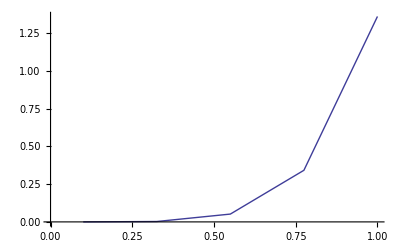

```mathematica
(* Now let's try to plot the error for 5th order expansion as a function of L*R. When there is perfect phasematching, then S and T go to 0. I am also setting L=1 to get a feel for how things scale. It should really be L*sqrt(R) that I investigate. *)
rulesplot :={ S -> 0, T -> 0,L->1,  N -> 1}
IE:=IntResultExact //.rulesplot
diff5plot := (IntResult9-IE)/IE //.rulesplot


(*data = Table[Abs[diff3plot*100], {R,.1, 1, .3}, {L,1, 2,.5}]
ListDensityPlot[data](*,  DataRange->{.1,1}]*)*)

data = Table[Abs[diff5plot*100], {R,.1, 2, .4}]
ListLinePlot[data, DataRange->{.1,1}]
(*Plot[Abs[diff3plot*100], {R, .1, 2}]*)
```

```mathematica
(* So it looks like the 5th order expansion is fine as long as L*R^0.5 << 1. Is there a better way to expand this without needing to go to a ton of terms? I tried it with the third order expansion and 9th order expansion. 
*)
```